# 3 body Hamiltonian

#### Definitions

```mathematica
Clear[b]
```

```mathematica
αβγ[b_]:={-((b[[1]]+b[[2]])/4+b[[3]]),-(b[[1]]+b[[2]]),(b[[1]]-b[[2]])/2}
```

```mathematica
Expand[α β-γ^2/.{α->-((b1+b2)/4+b3),β->-(b1+b2),γ->(b1-b2)/2}]
```

b1 b2+b1 b3+b2 b3

```mathematica
pow=1;
```

```mathematica
Solve[{α==-((b1+b2)/4+b3),β==-(b1+b2),γ==(b1-b2)/2},{b1,b2,b3}]
```

{{b1→1/2 (-β+2 γ),b2→1/2 (-β-2 γ),b3→-α+β/4}}

```mathematica
int[α_]:=(√(2/π)NIntegrate[r^2 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞}])
```

```mathematica
intp[α_]:=(√(2/π)α^(3/2) NIntegrate[r^2 Exp[-α r^2/2]/Cosh[r^pow],{r,0,∞}])
```

Check this integral for α very large (should be one)

```mathematica
int[99999999]
```

1.

```mathematica
Clear[α]
```

```mathematica
as=AsymptoticIntegrate[√(2/π)r^2 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞},{α,∞,30}];
```

```mathematica
ass=PadeApproximant[as,{α,∞,{14,15}}];
```

```mathematica
ass=N[ass]
```

(1.+(2.28903×10^10)/α^14+(2.55033×10^12)/α^13+(7.27493×10^12)/α^12+(8.08866×10^12)/α^11+(4.74551×10^12)/α^10+(1.67237×10^12)/α^9+(3.79697×10^11)/α^8+(5.78329×10^10)/α^7+(6.04099×10^9)/α^6+(4.36137×10^8)/α^5+(2.16338×10^7)/α^4+720572./α^3+15332.9/α^2+187.58/α)/(1.+(1.41453×10^11)/α^15+(3.10256×10^12)/α^14+(1.14729×10^13)/α^13+(1.76328×10^13)/α^12+(1.43999×10^13)/α^11+(7.03691×10^12)/α^10+(2.20465×10^12)/α^9+(4.62202×10^11)/α^8+(6.65676×10^10)/α^7+(6.67818×10^9)/α^6+(4.67999×10^8)/α^5+(2.27018×10^7)/α^4+743410./α^3+15613.4/α^2+189.08/α)

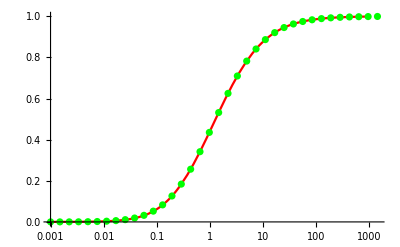

```mathematica
Block[{α},Show[{LogLinearPlot[N[ass],{α,0.001,1000}, PlotStyle->Red],ListLogLinearPlot[Table[{α=0.001 1.5^i,int[α]},{i,0,35}],PlotStyle->Green]},PlotRange->All]]
```

```mathematica
int[α_]=ass
```

(1.+(2.28903×10^10)/α^14+(2.55033×10^12)/α^13+(7.27493×10^12)/α^12+(8.08866×10^12)/α^11+(4.74551×10^12)/α^10+(1.67237×10^12)/α^9+(3.79697×10^11)/α^8+(5.78329×10^10)/α^7+(6.04099×10^9)/α^6+(4.36137×10^8)/α^5+(2.16338×10^7)/α^4+720572./α^3+15332.9/α^2+187.58/α)/(1.+(1.41453×10^11)/α^15+(3.10256×10^12)/α^14+(1.14729×10^13)/α^13+(1.76328×10^13)/α^12+(1.43999×10^13)/α^11+(7.03691×10^12)/α^10+(2.20465×10^12)/α^9+(4.62202×10^11)/α^8+(6.65676×10^10)/α^7+(6.67818×10^9)/α^6+(4.67999×10^8)/α^5+(2.27018×10^7)/α^4+743410./α^3+15613.4/α^2+189.08/α)

```mathematica
int2[α_]:=(1/3/√(π/2)NIntegrate[r^4 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞}])
```

```mathematica
as2=AsymptoticIntegrate[1/3/√(π/2)r^4 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞},{α,∞,30}];
```

```mathematica
ass2=PadeApproximant[as2,{α,∞,{14,15}}];
```

```mathematica
ass2=N[ass2]
```

(1.-(1.64435×10^11)/α^14+(9.33855×10^12)/α^13+(2.29001×10^13)/α^12+(2.19496×10^13)/α^11+(1.12652×10^13)/α^10+(3.5188×10^12)/α^9+(7.1591×10^11)/α^8+(9.86128×10^10)/α^7+(9.3882×10^9)/α^6+(6.21908×10^8)/α^5+(2.84712×10^7)/α^4+879744./α^3+17445.9/α^2+199.721/α)/(1.+(3.54648×10^12)/α^15+(2.78821×10^13)/α^14+(6.64773×10^13)/α^13+(7.55456×10^13)/α^12+(4.8822×10^13)/α^11+(1.96967×10^13)/α^10+(5.24638×10^12)/α^9+(9.55589×10^11)/α^8+(1.21579×10^11)/α^7+(1.0918×10^10)/α^6+(6.92266×10^8)/α^5+(3.06535×10^7)/α^4+923157./α^3+17944.2/α^2+202.221/α)

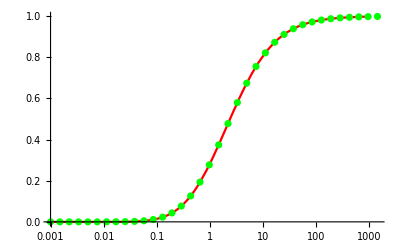

```mathematica
Block[{α},Show[{LogLinearPlot[N[ass2],{α,0.001,1000}, PlotStyle->Red],ListLogLinearPlot[Table[{α=0.001 1.5^i,int2[α]},{i,0,35}],PlotStyle->Green]},PlotRange->All]]
```

```mathematica
int2[α_]=ass2
```

(1.-(1.64435×10^11)/α^14+(9.33855×10^12)/α^13+(2.29001×10^13)/α^12+(2.19496×10^13)/α^11+(1.12652×10^13)/α^10+(3.5188×10^12)/α^9+(7.1591×10^11)/α^8+(9.86128×10^10)/α^7+(9.3882×10^9)/α^6+(6.21908×10^8)/α^5+(2.84712×10^7)/α^4+879744./α^3+17445.9/α^2+199.721/α)/(1.+(3.54648×10^12)/α^15+(2.78821×10^13)/α^14+(6.64773×10^13)/α^13+(7.55456×10^13)/α^12+(4.8822×10^13)/α^11+(1.96967×10^13)/α^10+(5.24638×10^12)/α^9+(9.55589×10^11)/α^8+(1.21579×10^11)/α^7+(1.0918×10^10)/α^6+(6.92266×10^8)/α^5+(3.06535×10^7)/α^4+923157./α^3+17944.2/α^2+202.221/α)

```mathematica
detb[b_]:=b[[1]] b[[2]]+b[[2]] b[[3]]+b[[3]]b[[1]]
```

```mathematica
dαβγ[α_,β_,γ_]:=α β -γ^2
```

```mathematica
Clear[matrixel];matrixel[b_,bp_,λ0_:1.3,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,ovl,kin,pot, s,arg},
arg[bs_]:=-(bs⟦2⟧ bs⟦3⟧+bs⟦1⟧ (bs⟦2⟧+bs⟦3⟧))/(bs[[1]]+bs[[2]]);
bs=b+bp;
{α,β,γ}=αβγ[b];{αp,βp,γp}=αβγ[bp]; {αs,βs,γs}=αβγ[bs];
s={-λ0(λ0-1)/2,-λ0(λ0+1)/2,-λ0(λ0+1)/2};
ovl=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2);
kin=
3/4(3β βp αs+4 α αp βs-4(α γp^2+αp γ^2)-3(β γp^2+βp γ^2))/dαβγ[αs,βs,γs] ovl;
If[debug,Return[{ovl,kin,ovl int[arg[bs]],ovl  int[arg[RotateLeft[bs,1]]],ovl int[arg[RotateLeft[bs,2]]]}],
pot=ovl(Plus@@{s[[1]] int[arg[bs]],s[[2]] int[arg[RotateLeft[bs,1]]],s[[3]] int[arg[RotateLeft[bs,2]]]});
{ovl,kin+pot}]
]
```

```mathematica
Clear[ovlel];ovlel[b_,bp_,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,ovl,kin,pot, s,arg},
arg[bs_]:=-(bs⟦2⟧ bs⟦3⟧+bs⟦1⟧ (bs⟦2⟧+bs⟦3⟧))/(bs[[1]]+bs[[2]]);
bs=b+bp;
{α,β,γ}=αβγ[b];{αp,βp,γp}=αβγ[bp]; {αs,βs,γs}=αβγ[bs];
ovl=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2)
]
```

### L = 1

```mathematica
dαβγc[α_,β_,γ_,cmm_,cpp_,cmp_]:=If[γ==0.,(cmm β+cpp α-cmp 10^-9)/(α β),(cmm β+cpp α-cmp γ)/(α β-γ^2) ]
```

```mathematica
?dαβγ
```

```mathematica
Clear[ctopm];ctopm[c_]:={c[[3]],(c[[2]]-c[[1]])/2}
```

```mathematica
Table[RotateLeft[{b1,b2,b3},i-1],{i,3}]
```

{{b1,b2,b3},{b2,b3,b1},{b3,b1,b2}}

```mathematica
Simplify[αβγ/@Table[RotateLeft[{b,b,x},i-1],{i,3}]]
```

{{-b/2-x,-2 b,0},{1/4 (-5 b-x),-b-x,(b-x)/2},{1/4 (-5 b-x),-b-x,1/2 (-b+x)}}

```mathematica
Clear[matrixel1];matrixel1[bc_,bcp_,λ0_:1.3,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,cp,cm,cpp,cpm,ovl,ovl0,kin,pot, s,v2},
bs=bc[[1]]+bcp[[1]];
{α,β,γ}=αβγ[bc[[1]]];{αp,βp,γp}=αβγ[bcp[[1]]]; {αs,βs,γs}=αβγ[bs];
{cp,cm}=ctopm[bc[[2]]];{cpp,cpm}=ctopm[bcp[[2]]];
s={-λ0(λ0-1)/2,-λ0(λ0+1)/2,-λ0(λ0+1)/2};
v2[bs_,c1i_,c2i_]:=Block[{cpi,cmi,cppi,cpmi,αsi,βsi,γsi,ϵ,δ},{αsi,βsi,γsi}=αβγ[bs];{cpi,cmi}=ctopm[c1i];{cppi,cpmi}=ctopm[c2i];δ=αsi-γsi^2/βsi;ϵ=(cmi βsi-cpi γsi)(cpmi βsi-cppi γsi)/βsi;(*Print[{c1i,c2i,αsi,βsi,γsi,δ,ϵ, cpi cppi, int[δ],int2[δ]}];*)(*(cpi cppi δ int[δ]+ ϵ int2[δ])/(cpi cppi δ +ϵ)*)(cpi cppi δ int[δ]+ ϵ int2[δ])/dαβγ[αsi,βsi,γsi]];

ovl0=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2)/(dαβγc[2α,2β,2γ,cm cm,cp cp,2cm cp]^(1/2)dαβγc[2αp,2βp,2γp,cpm cpm,cpp cpp,2cpm cpp]^(1/2));
ovl=ovl0
dαβγc[α+αp,β+βp,γ+γp,cm cpm,cp cpp,cpm cp+cm cpp];
kin=
(cm cpp (8 αp^2 (β+βp) γ+3 (γ+γp) (3 βp γ^2+β γp (-2 γ+γp))+(α+αp) (6 β^2 γp-3 β βp (3 γ+γp))+4 (γ+γp) (αp γ (γ-2 γp)+3 α γp^2)-4α αp (β+βp) (γ+3 γp))+cm cpm (-3 βp (β+3 βp) γ^2-3 β (3 β+βp) γp^2+12 γ  β βp γp+8 γ γp (γ+γp)^2+3 (α+αp)(β+βp) β βp-12 (β+βp) ( αp γ^2+ α γp^2)-8 (α+αp) (β+βp)γ γp  +12α αp(β+βp)^2)+cp cpp (-3(α+αp) (3 βp γ^2+2 (β+βp) γ γp+3 β γp^2)+9(α+αp)^2 ( β βp)-12( γ^2 αp^2+α^2 γp^2)+4α αp(α+αp) (β+βp)+6 γ γp (γ+γp)^2-4α  αp (γ^2-4 γ γp+γp^2))+cp cpm (-α βp(-6 βp γ)-α βp(3 β (γ+3 γp))+3αp βp (2 βp γ-β (γ+3 γp))+4 (γ+γp) (3 αp γ^2+α γp (-2 γ+γp))+8 α^2 (β+βp) γp-4α  αp (β+βp) (3 γ+γp)+3 (γ+γp) (βp γ (γ-2 γp)+3 β γp^2)))/(4 ((α +αp) (β+βp)-(γ+γp)^2)^2)ovl0+1/2(3β βp αs+4 α αp βs-4(α γp^2+αp γ^2)-3(β γp^2+βp γ^2))/dαβγ[αs,βs,γs] ovl;
If[debug,Print[{ovl,kin,Table[ovl0  v2[RotateLeft[bs,i-1],RotateLeft[bc[[2]],i-1],RotateLeft[bcp[[2]],i-1]],{i,3}]}],pot=ovl0(Plus@@Table[ s[[i]] v2[RotateLeft[bs,i-1],RotateLeft[bc[[2]],i-1],RotateLeft[bcp[[2]],i-1]],{i,3}]);{ovl,kin+pot}]
]
```

```mathematica
Clear[ovlel1];ovlel1[bc_,bcp_,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,cp,cm,cpp,cpm,ovl,ovl0,kin,pot, s,v2},
bs=bc[[1]]+bcp[[1]];
{α,β,γ}=αβγ[bc[[1]]];{αp,βp,γp}=αβγ[bcp[[1]]]; {αs,βs,γs}=αβγ[bs];
{cp,cm}=ctopm[bc[[2]]];{cpp,cpm}=ctopm[bcp[[2]]];
ovl0=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2)/(dαβγc[2α,2β,2γ,cm cm,cp cp,2cm cp]^(1/2)dαβγc[2αp,2βp,2γp,cpm cpm,cpp cpp,2cpm cpp]^(1/2));
ovl=ovl0
dαβγc[α+αp,β+βp,γ+γp,cm cpm,cp cpp,cpm cp+cm cpp]
]
```

## Calculation

### L=0

```mathematica
bs=Block[{t},t=Table[-0.002 3.3^i, {i,5}];DeleteCases[Flatten[Outer[List,t,t,t],2],{a_,b_,c_}/;a>b]];
```

```mathematica
p12[bs_]:={bs[[2]],bs[[1]],bs[[3]]}
```

```mathematica
mm=Outer[((matrixel[#1,#2,1.5]+matrixel[#1,p12[#2],1.5])/Sqrt[(1.+ovlel[#2,p12[#2]])(1.+ovlel[#1,p12[#1]])])&,bs,bs,1];
```

```mathematica
ov=Map[#[[1]]&,mm,{2}];
```

```mathematica
ham=Map[#[[2]]&,mm,{2}];
```

```mathematica
Chop[SparseArray[ham-Transpose[ham]]]
```

SparseArray[…]

```mathematica
ham[[1,2]]
```

-0.00164164

```mathematica
ham[[2,1]]
```

-0.00164164

```mathematica
Eigenvalues[ov]
```

{37.0299,13.5583,8.22774,4.65429,2.68111,2.63653,1.47268,1.07607,0.771521,0.658123,0.445934,0.402253,0.247133,0.203502,0.185873,0.14044,0.121545,0.110998,0.0684196,0.0503936,0.0444366,0.0344053,0.030936,0.0278507,0.0179314,0.0172612,0.0146164,0.012228,0.0104238,0.00854554,0.00604624,0.00572579,0.0040874,0.003584,0.00339294,0.00263685,0.00219635,0.00191227,0.00169002,0.00121473,0.000975429,0.000941114,0.000818608,0.000600533,0.000510031,0.0004481,0.000313722,0.00026922,0.000218753,0.000208209,0.000165713,0.000141659,0.000113431,0.0000933833,0.0000621275,0.0000561796,0.0000464914,0.0000292326,0.0000269458,0.0000221251,0.0000126987,9.67641×10^-6,9.27146×10^-6,7.20815×10^-6,4.93587×10^-6,4.04285×10^-6,3.13404×10^-6,2.10694×10^-6,1.35129×10^-6,9.5237×10^-7,1.71055×10^-7,1.13142×10^-7,9.88187×10^-8,5.9113×10^-9,3.15289×10^-9}

```mathematica
evs=Sort[Eigenvalues[{ham,ov}]]
```

{-0.519835,-0.182729,-0.146256,-0.059875,0.0270131,0.0611891,0.0904237,0.112593,0.119889,0.148889,0.176054,0.205331,0.235149,0.267809,0.321275,0.348688,0.388189,0.422456,0.441372,0.482195,0.53122,0.552153,0.595878,0.646768,0.674566,0.736151,0.760639,0.787135,0.911444,0.947572,1.01979,1.12926,1.16915,1.23884,1.30198,1.38873,1.49297,1.55968,1.63489,1.63814,1.72069,1.74749,1.96819,2.06818,2.09625,2.11699,2.22876,2.25659,2.33958,2.45354,2.48795,2.5566,2.7052,2.85576,2.9398,2.96968,3.07929,3.28946,3.41636,3.55268,3.77476,4.01135,4.08866,4.43434,4.53306,4.88022,5.00087,5.28194,5.40646,6.39572,6.53053,7.10163,7.93273,8.19433,8.37364}

```mathematica
ind=Table[i,{i,Length[evs]}]-1;
```

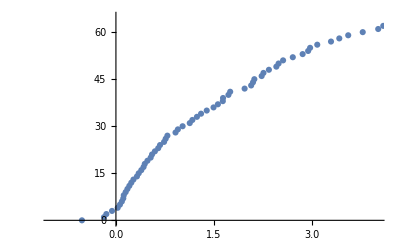

```mathematica
ListPlot[Transpose[{evs,ind}],PlotRange->{{-1,4},{-0.5,65}},PlotMarkers->Automatic]
```

```mathematica
gs=Sort[Transpose[Eigensystem[{ham,ov}]],#1[[1]]<#2[[1]]&][[1]]
```

{-0.519835,{-9.48046×10^-6,0.0000332456,-0.0000933419,0.000138366,-0.000066629,0.0000676464,-0.000225431,0.000581325,-0.000824488,0.00050553,-0.000119383,0.000362381,-0.000886001,0.00113562,-0.00103339,-0.000122457,0.000516391,-0.001448,0.00238097,0.00162744,0.00036378,-0.00178669,0.00353076,-0.00534412,-0.00043844,0.000159026,-0.000185992,-0.00471963,0.00323104,-0.00124851,0.0000893937,-0.00051286,0.00258271,-0.00840248,-0.0235242,-4.96618×10^-6,0.000340636,-0.00576903,0.0176131,0.0349812,-0.000232609,-0.0013162,-0.00270148,-0.0163828,-0.011696,0.000777155,0.00042503,-0.0081167,0.00321546,0.000108235,-0.000136574,0.000701152,-0.0012616,-0.00676369,-0.525324,0.000309004,-0.00203021,0.00372822,0.00950059,0.782194,0.00113141,-0.000343522,-0.00824365,-0.000597518,-0.295977,-0.0412246,0.066678,-0.0316754,-0.00214797,0.0422372,-0.0652813,0.0884755,-0.0236057,-0.000511817,-0.00337087}}

```mathematica
gs=gs[[2]]/Sqrt[gs[[2]].(ov.gs[[2]])]
```

{-0.000296912,0.0010412,-0.00292331,0.00433338,-0.00208671,0.00211857,-0.00706013,0.0182061,-0.0258216,0.0158324,-0.00373886,0.0113492,-0.027748,0.0355656,-0.032364,-0.00383514,0.0161725,-0.0453489,0.074568,0.0509687,0.011393,-0.0559559,0.110577,-0.167369,-0.0137312,0.00498042,-0.00582494,-0.147811,0.101191,-0.0391012,0.00279966,-0.0160619,0.0808862,-0.263151,-0.736738,-0.000155532,0.0106681,-0.180676,0.551613,1.09555,-0.00728492,-0.041221,-0.0846057,-0.51308,-0.366299,0.0243392,0.0133112,-0.254201,0.100703,0.00338973,-0.00427728,0.0219589,-0.039511,-0.211827,-16.4522,0.00967749,-0.0635827,0.116762,0.297542,24.497,0.0354338,-0.0107585,-0.258177,-0.0187132,-9.26948,-1.29108,2.08824,-0.992019,-0.0672709,1.3228,-2.0445,2.7709,-0.739291,-0.0160292,-0.10557}

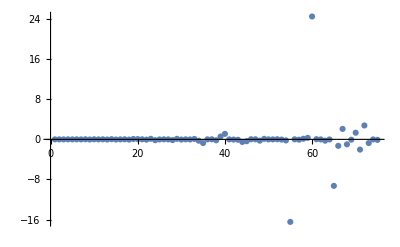

```mathematica
ListPlot[gs,PlotRange->All]
```

### L=1

```mathematica
cs={{1/2,1/2,-1},{-1,1,0}}
```

{{1/2,1/2,-1},{-1,1,0}}

```mathematica
bs1=Block[{t},t=Table[-0.002 3.3^i, {i,5}];Select[Flatten[Outer[List,t,t,t],2],#[[1]]<#[[2]]&]];
```

```mathematica
matrixel1[{bs1[[1]],cs[[2]]},{bs1[[1]],cs[[1]]}]
```

{-0.384995,-0.000464151}

```mathematica
bcs=Flatten[Outer[List,bs1,cs,1],1];
```

```mathematica
p121[bcs_]:={{bcs[[1,2]],bcs[[1,1]],bcs[[1,3]]},{bcs[[2,2]],bcs[[2,1]],bcs[[2,3]]}}
```

```mathematica
mm1=Outer[((matrixel1[#1,#2,1.5]+matrixel1[#1,p121[#2],1.5])/Sqrt[(1.+ovlel1[#2,p121[#2]])(1.+ovlel1[#1,p121[#1]])])&,bcs,bcs,1];
```

```mathematica
ov1=Map[#[[1]]&,mm1,{2}];
```

```mathematica
Take[ArrayRules[SparseArray[Chop[ov1-Transpose[ov1]]]],10]
```

{{1,2}→-4.57305×10^-8,{1,4}→-6.06163×10^-8,{1,6}→-5.25691×10^-8,{1,8}→-2.97902×10^-8,{1,10}→-1.36334×10^-8,{2,1}→4.57305×10^-8,{2,3}→2.82875×10^-8,{2,5}→8.87726×10^-9,{2,7}→1.61936×10^-9,{2,9}→2.28889×10^-10}

```mathematica
bcs[[1]]
```

{{-0.02178,-0.0066,-0.0066},{1/2,1/2,-1}}

```mathematica
bcs[[12]]
```

{{-0.071874,-0.0066,-0.0066},{-1,1,0}}

```mathematica
ov1[[;;10,;;10]]//MatrixForm
```

(1. | -0.518358 | 0.880933 | -0.591085 | 0.557991 | -0.446286 | 0.272932 | -0.235254 | 0.118524 | -0.104796
-0.518358 | 1. | -0.275838 | 0.764944 | -0.0753636 | 0.276106 | -0.0127882 | 0.0534064 | -0.00175941 | 0.00769997
0.880933 | -0.275838 | 1. | -0.479755 | 0.820911 | -0.559872 | 0.466103 | -0.379019 | 0.214649 | -0.186247
-0.591085 | 0.764944 | -0.479755 | 1. | -0.202597 | 0.640774 | -0.0441497 | 0.174248 | -0.00670048 | 0.0287827
0.557991 | -0.0753637 | 0.820911 | -0.202597 | 1. | -0.458857 | 0.79196 | -0.542636 | 0.430611 | -0.351965
-0.446286 | 0.276106 | -0.559872 | 0.640774 | -0.458857 | 1. | -0.174675 | 0.583576 | -0.0349922 | 0.141676
0.272932 | -0.0127882 | 0.466103 | -0.0441497 | 0.79196 | -0.174675 | 1. | -0.450945 | 0.781503 | -0.536156
-0.235254 | 0.0534064 | -0.379019 | 0.174248 | -0.542636 | 0.583576 | -0.450945 | 1. | -0.165592 | 0.563586
0.118524 | -0.00175941 | 0.214649 | -0.00670048 | 0.430611 | -0.0349922 | 0.781503 | -0.165592 | 1. | -0.448364
-0.104796 | 0.00769997 | -0.186247 | 0.0287827 | -0.351965 | 0.141676 | -0.536156 | 0.563586 | -0.448364 | 1.)

```mathematica
Eigenvalues[ov1]
```

{35.5417,15.9349,10.8805,7.01233,5.32841,4.16445,3.21965,2.75782,2.41259,1.97387,1.39851,1.31514,1.10895,0.939891,0.733004,0.703371,0.650002,0.502744,0.435128,0.391251,0.313813,0.277722,0.268396,0.22345,0.20761,0.155343,0.140435,0.13769,0.102121,0.0902001,0.085332,0.0787859,0.0658047,0.0594539,0.0480693,0.0432517,0.0420438,0.0293144,0.0278201,0.0254435,0.020388,0.0179857,0.0168647,0.014827,0.0141356,0.0107211,0.00932862,0.00885458,0.00772555,0.00678712,0.00586749,0.00513294,0.00500383,0.00394097,0.0035227,0.00278879,0.00223564,0.00216824,0.00205705,0.00180664,0.00160882,0.00138178,0.0011337,0.000980344,0.00090503,0.000805143,0.000727205,0.000623977,0.000557047,0.000515153,0.000372206,0.000305899,0.000299342,0.000223763,0.000204867,0.000158124,0.000142142,0.00012892,0.000106901,0.0000906623,0.0000814478,0.0000570675,0.0000391461,0.0000362033,0.0000317066,0.0000236525,0.0000226078,0.0000167718,0.0000118018,7.22265×10^-6,3.71282×10^-6,2.94852×10^-6,2.30223×10^-6,1.88421×10^-6,1.43696×10^-6,1.19492×10^-6,2.07889×10^-7,1.54221×10^-7,6.22915×10^-8,1.36102×10^-8}

```mathematica
ham1=Map[#[[2]]&,mm1,{2}];
```

```mathematica
ev1=Sort[Eigenvalues[{ham1,ov1}]]
```

{-0.171616,-0.126106,-0.0480131,0.0604111,0.0705095,0.100198,0.1059,0.162097,0.197493,0.210679,0.248391,0.261637,0.278601,0.305627,0.330623,0.367122,0.369809,0.396408,0.408264,0.517646,0.541676,0.554802,0.597196,0.629225,0.647638,0.666582,0.696157,0.701973,0.716938,0.757289,0.811348,0.839963,0.947711,0.957304,1.023,1.04695,1.11334,1.15429,1.21137,1.27873,1.31638,1.33045,1.40277,1.42211,1.48387,1.50071,1.54769,1.66398,1.70172,1.84035,1.9237,1.99037,2.08239,2.11696,2.12724,2.1651,2.18534,2.23997,2.26691,2.35113,2.35982,2.4641,2.51636,2.53866,2.64749,2.67553,2.79185,2.8736,2.92766,2.98251,3.02747,3.12923,3.23002,3.32636,3.38558,3.47787,3.51565,3.56178,3.76294,3.81716,3.9369,3.96448,4.04895,4.09032,4.31753,4.54395,4.67092,4.75595,5.07059,5.29728,5.36673,5.63676,5.87312,6.06087,6.31743,6.51118,6.64717,7.28951,8.26352,9.06898}

```mathematica
ind=Table[i,{i,Length[ev1]}]-1;
```

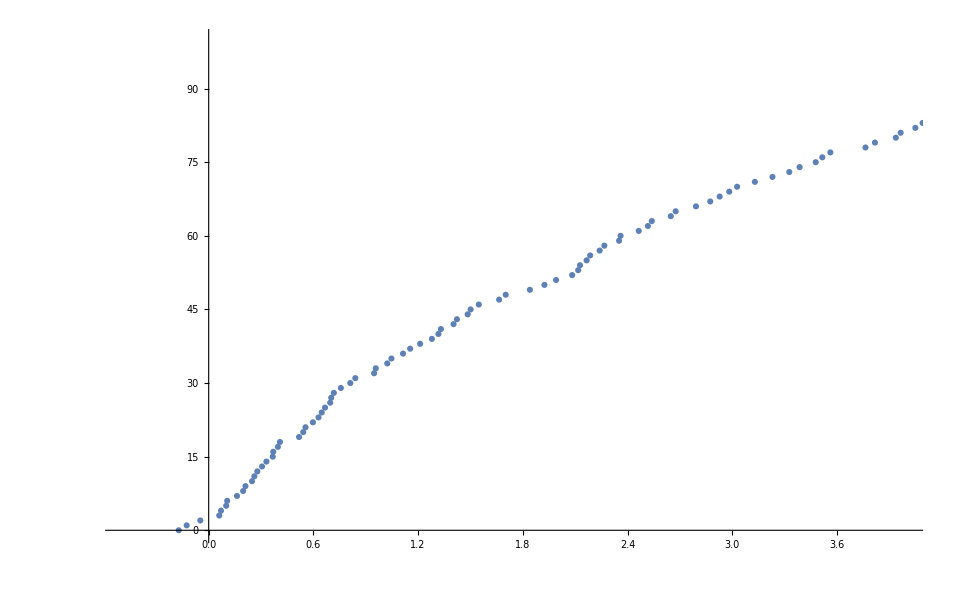

```mathematica
ListPlot[Transpose[{ev1,ind}],PlotRange->{{-0.5,4},{-0.5,100}},PlotMarkers->Automatic]
```

```mathematica
ov1=(ov1+Transpose[ov1])/2;ham1=(ham1+Transpose[ham1])/2;
```

```mathematica
sel[min_:0]:=Block[{mt=Eigensystem[ov1],evl,trf,dg}, {evl,trf}=Transpose[Select[Transpose[mt],#[[1]]>min&]];dg=DiagonalMatrix[1/Sqrt[evl]];Sort[Eigenvalues[dg.trf.ham1.Transpose[trf].dg]]]
```

```mathematica
sel[10^-4]
```

{-0.171514,-0.125631,-0.046681,0.0609488,0.0737299,0.100337,0.106174,0.162723,0.197768,0.212898,0.250523,0.262773,0.288987,0.309996,0.334639,0.371408,0.372434,0.398041,0.412644,0.524174,0.547603,0.56283,0.601937,0.656842,0.667723,0.692802,0.720196,0.724672,0.761002,0.833451,0.869101,0.932693,0.971593,1.03607,1.09228,1.12341,1.22275,1.23678,1.27317,1.43379,1.48352,1.50276,1.56163,1.59455,1.71598,1.86042,1.92518,2.04347,2.08857,2.11878,2.14906,2.18235,2.23435,2.29178,2.34713,2.4473,2.49877,2.55216,2.62011,2.8006,2.90371,3.03414,3.16167,3.27736,3.3263,3.4751,3.53313,3.64746,3.8837,4.01434,4.14084,4.50842,4.63958,4.79177,4.93053,5.48679,5.64535,6.74431,7.41604}

```mathematica
sel[min_:0]:=Block[{mt=Eigensystem[ov1],evl,trf,dg,es,evs}, {evl,trf}=Transpose[Select[Transpose[mt],#[[1]]>min&]];dg=DiagonalMatrix[1/Sqrt[evl]];{es,evs}=Eigensystem[dg.trf.ham1.Transpose[trf].dg];{es,Transpose[trf].dg.evs}]
```

```mathematica
{ess,evss}=sel[0];
```

{{1.89593,0.301989,0.148304,-0.20368,-1.62576,0.969328,-0.635583,0.853194,0.187445,-0.153982,0.0681993,0.433482,0.105833,0.334259,-0.884446,0.359823,-1.0806,66,-0.176757,-0.143047,0.159387,-0.111244,-0.315988,0.00651219,-0.798398,0.0720982,-0.286773,0.219746,0.450605,0.246079,-0.427087,0.316573,0.553896,-0.0682387,0.296017},98,{1}}
 |  |  |  |

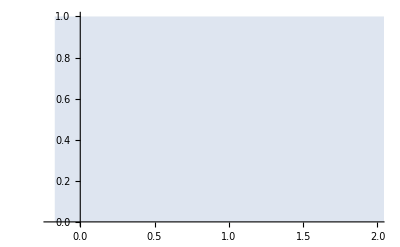

```mathematica
sm=0;ListLinePlot[{#[[1]],sm+=#[[2]]}&/@Sort[Transpose[{ess,(#.rhs)^2&/@evss}],#⟦1⟧<#2⟦1⟧&],PlotMarkers->"OpenMarkers",Filling->Axis,PlotRange->{{-0.2,2},{0,1}}]
```

## LIT

```mathematica
Clear[ovl];ovl[bc_,bp_,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,cp,cm,cpp,cpm,ovl,ovl0,kin,pot, s,λ0=1.4,v2},
bs=bc[[1]]+bp;
{α,β,γ}=αβγ[bc[[1]]];{αp,βp,γp}=αβγ[bp]; {αs,βs,γs}=αβγ[bs];
{cp,cm}=ctopm[bc[[2]]];{cpp,cpm}={2/3,0};

ovl0=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2)/(dαβγc[2α,2β,2γ,cm cm,cp cp,2cm cp]^(1/2));
ovl0
dαβγc[α+αp,β+βp,γ+γp,cm cpm,cp cpp,cpm cp+cm cpp]
]
```

```mathematica
ovmat=Outer[(ovl[#1,#2]+ovl[#1,p12[#2]])/Sqrt[(1.+ovlel1[#1,p121[#1]])(1.+ovlel[#2,p12[#2]])]&,bcs,bs,1];
```

```mathematica
rhs=ovmat.gs
```

{0.0908253,-0.0149815,0.137049,-0.0380539,0.182545,-0.0848518,0.172452,-0.112506,0.112378,-0.0874179,0.176529,-0.0417761,0.28631,-0.0884765,0.399584,-0.183455,0.393964,-0.251891,0.265592,-0.205135,0.305824,-0.0761664,0.378094,-0.121686,0.462379,-0.21539,0.443282,-0.284143,0.29904,-0.231055,0.189081,-0.0776616,0.362553,-0.153056,0.603927,-0.292364,0.649032,-0.401215,0.458368,-0.34554,0.37333,-0.143133,0.492105,-0.200859,0.650219,-0.314094,0.658299,-0.408219,0.463591,-0.349934,0.624036,-0.237253,0.660439,-0.272349,0.708549,-0.348784,0.669432,-0.418958,0.473622,-0.358378,0.126337,-0.0819305,0.257795,-0.162454,0.503677,-0.305416,0.634145,-0.399214,0.469026,-0.340606,0.258312,-0.158902,0.3605,-0.217869,0.546727,-0.32444,0.631992,-0.39668,0.463324,-0.336849,0.504583,-0.27899,0.546261,-0.303176,0.617087,-0.351096,0.615041,-0.384666,0.44494,-0.324713,0.596849,-0.314369,0.595641,-0.319718,0.585571,-0.331558,0.531977,-0.337871,0.391794,-0.289047}

```mathematica
es=Eigensystem[{ham1,ov1}];
```

```mathematica
evs=Table[es[[2,i]]/Sqrt[es[[2,i]].ov1.es[[2,i]]],{i,Length[es[[1]]]}]
```

{{-0.00483141,-0.00271366,0.0114171,0.0122439,-0.0114223,-0.0383528,0.061483,0.128428,-0.0202776,0.0136478,-0.0334455,0.055639,0.0795702,-0.229901,-0.00892083,0.736377,-0.931896,66,-2.90407,-1.53625,0.822721,-9.9198,-33.2172,661.374,1087.4,-45.9715,-9.88284,66.3078,14.677,-23.4813,-5.76622,4.68148,4.26871,-68.2772,-106.811},98,{1}}
 |  |  |  |

```mathematica
Length[evs[[1]]]
```

100

```mathematica
Sort[Transpose[es],#⟦1⟧<#2⟦1⟧&][[;;2]]
```

{{-0.171616,{-0.00238259,0.00500364,0.00061298,-0.00100302,-0.0000884354,-0.000116005,-0.0000729701,0.000306436,8.75377×10^-7,-0.0000107691,-0.0380681,0.090226,0.0174514,-0.0553486,0.00151974,0.0207697,-0.00283288,-0.00755762,0.000197372,-0.000146428,0.0255843,-0.0408694,-0.0241963,0.0500983,0.000428484,-0.0248801,0.00298635,0.00923396,-0.000120831,0.000401235,-0.0594994,0.167516,0.0131236,-0.122006,0.0264755,0.0598144,-0.0170228,0.0235639,-0.015586,-0.0410795,0.0694034,-0.0827656,-0.0642976,0.138616,-0.0155033,-0.0964807,0.0221971,-0.0257651,0.0189315,0.0531771,-0.0702566,0.0204153,0.104624,-0.055617,-0.0360936,0.0528025,-0.00126214,-0.00383117,-0.00414672,-0.0122779,-0.0267164,0.0813675,0.0104512,-0.0686063,-0.0137231,-0.0721105,0.0762484,0.318473,0.134391,0.224085,0.0267439,-0.0513128,-0.0365506,0.113959,0.0334267,0.0587335,-0.115643,-0.452261,-0.179609,-0.291463,0.0465222,-0.0173623,-0.0497813,-0.0191126,-0.00305937,0.0112477,0.0441891,0.144205,0.0469691,0.0696326,-0.210813,0.19774,0.299016,-0.279066,-0.0966981,0.0884117,0.00377061,-0.0202607,-0.00177366,-0.00089962}},{-0.126106,{-0.000956432,-0.0024871,-0.000895182,0.0010016,-0.000135869,0.00027221,-0.000294282,-0.000395467,0.00002561,0.0000137665,0.0171486,-0.0437711,-0.0197316,0.0600255,0.000267612,-0.0228151,0.00508291,0.00876188,-0.000900444,0.000172284,-0.0275592,0.0439118,0.0260815,-0.0545648,-0.00434282,0.0268118,-0.00580025,-0.0103287,0.000806013,-0.000482384,0.0288519,-0.0813305,-0.0182504,0.131518,-0.0243889,-0.0604483,0.0108907,-0.0284531,0.00703318,0.0414356,-0.0730495,0.0935877,0.07173,-0.155075,0.0123124,0.0998497,-0.0116479,0.0321556,-0.00834595,-0.0536033,0.0682465,-0.0250008,-0.10556,0.0615896,0.0338633,-0.0552566,-0.00382632,0.00257462,0.00169957,0.0124381,0.0128467,-0.0405335,0.00260883,0.0857935,-0.0158017,0.0324111,-0.12842,-0.342933,-0.0439218,-0.193447,-0.0412629,0.0411922,0.0357874,-0.116858,0.011221,-0.00486244,0.179413,0.47929,0.05216,0.249193,-0.00869173,0.0379117,-0.00490718,-0.013056,0.00677436,-0.0163278,-0.0594281,-0.147311,-0.00651965,-0.0576021,0.260033,-0.173659,-0.362953,0.250486,0.112539,-0.0820814,-0.00418035,0.0194659,-0.0015985,0.000481239}}}

```mathematica
Sort[Transpose[{es[[1]],(#.rhs)^2&/@evs}],#⟦1⟧<#2⟦1⟧&]
```

{{-0.171616,0.00395094},{-0.126106,0.0392901},{-0.0480131,0.159889},{0.0604111,0.0281665},{0.0705095,0.180355},{0.100198,0.000874862},{0.1059,0.00541683},{0.162097,0.000656652},{0.197493,0.000168867},{0.210679,0.00055977},{0.248391,6.8396×10^-6},{0.261637,0.00103394},{0.278601,0.0626335},{0.305627,0.0243919},{0.330623,0.000918712},{0.367122,0.000279623},{0.369809,0.000424014},{0.396408,3.88782×10^-6},{0.408264,0.000831653},{0.517646,0.00214198},{0.541676,0.000511868},{0.554802,0.00541963},{0.597196,0.0000595666},{0.629225,0.00025731},{0.647638,0.004141},{0.666582,0.00194826},{0.696157,0.00122506},{0.701973,0.00544668},{0.716938,0.000680351},{0.757289,0.000919157},{0.811348,0.00167634},{0.839963,0.000837903},{0.947711,0.000414825},{0.957304,0.00019654},{1.023,0.000204579},{1.04695,0.0000580439},{1.11334,0.000342862},{1.15429,0.0000955274},{1.21137,0.000611446},{1.27873,0.0000521527},{1.31638,1.05899×10^-6},{1.33045,0.00103725},{1.40277,0.000736987},{1.42211,0.000366845},{1.48387,0.000018248},{1.50071,0.0000153426},{1.54769,8.93052×10^-7},{1.66398,0.0000211127},{1.70172,0.0000156939},{1.84035,0.000202004},{1.9237,0.000272052},{1.99037,0.000172181},{2.08239,5.20846×10^-6},{2.11696,9.64938×10^-6},{2.12724,0.0000260385},{2.1651,2.96171×10^-6},{2.18534,1.53866×10^-6},{2.23997,5.03155×10^-6},{2.26691,0.0000245541},{2.35113,0.0000506189},{2.35982,0.0000279293},{2.4641,0.0000403113},{2.51636,4.05669×10^-7},{2.53866,0.000113743},{2.64749,2.98608×10^-6},{2.67553,4.64611×10^-6},{2.79185,1.35682×10^-6},{2.8736,3.61061×10^-6},{2.92766,0.0000306113},{2.98251,8.6497×10^-7},{3.02747,4.99283×10^-7},{3.12923,0.0000160416},{3.23002,0.0000478312},{3.32636,0.0000399143},{3.38558,2.08109×10^-7},{3.47787,6.90976×10^-8},{3.51565,3.72763×10^-6},{3.56178,5.66046×10^-7},{3.76294,7.22852×10^-6},{3.81716,1.44917×10^-6},{3.9369,6.46377×10^-6},{3.96448,1.90802×10^-6},{4.04895,5.27058×10^-7},{4.09032,2.57634×10^-6},{4.31753,1.16482×10^-9},{4.54395,2.58265×10^-6},{4.67092,1.29386×10^-6},{4.75595,3.92556×10^-6},{5.07059,3.01764×10^-7},{5.29728,1.2317×10^-6},{5.36673,1.33852×10^-6},{5.63676,4.43091×10^-7},{5.87312,1.40524×10^-8},{6.06087,7.51011×10^-7},{6.31743,3.86861×10^-8},{6.51118,4.72134×10^-7},{6.64717,1.20753×10^-10},{7.28951,1.89615×10^-7},{8.26352,1.98205×10^-7},{9.06898,1.05782×10^-6}}

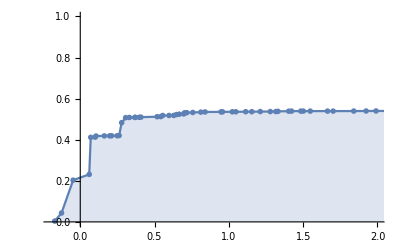

```mathematica
sm=0;ListLinePlot[{#[[1]],sm+=#[[2]]}&/@Sort[Transpose[{es[[1]],(#.rhs)^2&/@evs}],#⟦1⟧<#2⟦1⟧&],PlotMarkers->"OpenMarkers",Filling->Axis,PlotRange->{{-0.2,2},{0,1}}]
```

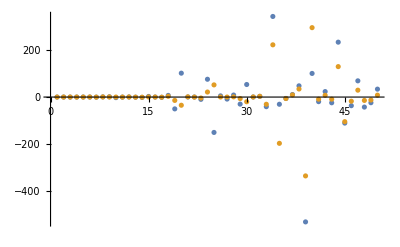

```mathematica
ListPlot[{evs[[5,;;;;2]],evs[[5,2;;;;2]]},PlotRange->All]
```

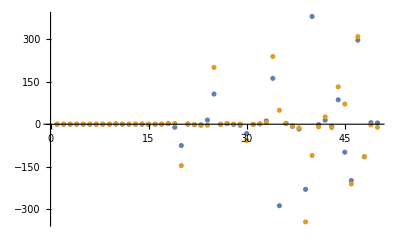

```mathematica
ListPlot[{evs[[6,;;;;2]],evs[[6,2;;;;2]]},PlotRange->All]
```

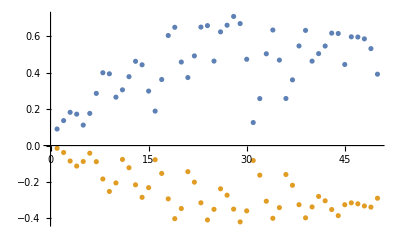

```mathematica
ListPlot[{rhs[[;;;;2]],rhs[[2;;;;2]]},PlotRange->All]
```

```mathematica
Table[1/(evs[[i]].evs[[i]]),{i,100}]
```

{4.60125×10^-8,1.21611×10^-7,8.19963×10^-8,4.34297×10^-8,1.16146×10^-6,1.08949×10^-6,8.98496×10^-8,2.97762×10^-7,1.06869×10^-6,7.10669×10^-7,4.14034×10^-7,5.23203×10^-7,1.40298×10^-6,1.07289×10^-6,1.78676×10^-7,1.18916×10^-6,8.52143×10^-7,4.01103×10^-6,1.71814×10^-6,1.35838×10^-6,1.6799×10^-6,2.3888×10^-6,7.72007×10^-6,5.6177×10^-6,0.0000125706,1.19804×10^-6,8.70252×10^-7,1.75811×10^-6,2.78548×10^-6,5.76312×10^-6,0.0000171731,6.30612×10^-6,7.52618×10^-6,7.9362×10^-6,0.0000178958,0.0000169788,7.04295×10^-6,0.0000131927,7.53863×10^-6,0.0000116775,6.20075×10^-6,0.0000132258,0.0000180447,0.0000232126,0.0000586399,0.0000277393,0.0000610673,0.0000364975,5.00045×10^-6,0.0000161237,0.0000112718,0.0000188754,0.0000284829,0.0000604941,0.000105144,0.000120121,0.0000120264,0.0000207286,0.0000252275,0.000045284,0.000100141,0.0000198394,0.000120072,0.0000734753,0.0000842171,0.0000790282,0.0000563533,0.000390878,0.000164337,0.000178321,0.000132662,0.000290073,0.000210501,0.000286722,0.000274373,0.000151567,0.000239281,0.000833893,0.000197489,0.000506801,0.000346353,0.000873469,0.00130763,0.00135199,0.00184574,0.0016283,0.000705744,0.000374248,0.00215513,0.0020426,0.00373718,0.00710012,0.0445164,0.00996781,0.00905644,0.00980824,0.0321116,0.00126853,0.00658511,0.00307951}

```mathematica
1/(evs[[6]].evs[[6]])
```

1.08949×10^-6

```mathematica
bcs[[1,;;;;2]]
```

{{-0.02178,-0.0066,-0.0066}}